# Find Slow-Roll Parameters from Deformed Quad Potential

## The D-SRP code is outlined below and follows some of the steps mentioned in the excerpt above.

To start, let’s import the data D-SRP calculation in python.

InterpolatingFunction[…]

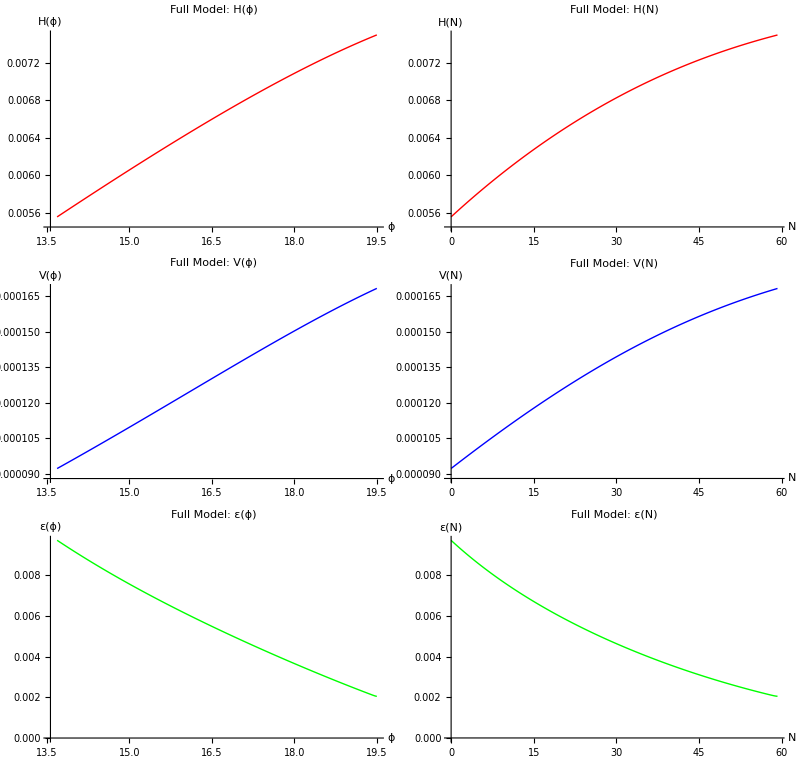

```mathematica
data=Import["/Users/epmeador/Desktop/research/rwarthur/inflation_gravitywaves/inflation_code/Slow-Roll Parameters Tests/phi_H_V_N_clean_deformed_quad.csv","CSV"];;
headers=data[[1]];
numericalData=data[[2;;]];

(*These are the variables in order from large to small or rather early to late times*)
ϕvals=numericalData[[All,1]];(*large to small*)
Hvals=numericalData[[All,2]];(*large to small*)
Vvals=numericalData[[All,3]];
Nvals=numericalData[[All,4]];

(*I am going to reverse the order so we start with late times (N=0) to early times*)

ϕvals = Reverse[ϕvals]; 
Vvals = Reverse[Vvals];
Hvals = Reverse[Hvals];
Nvals = Reverse[Nvals];

(*Define epsilon using H and derivative of H*)
HInterp=Interpolation[Transpose[{ϕvals,Hvals}],InterpolationOrder->3]
epsdyn[ϕ_]:=2 (HInterp'[ϕ]/HInterp[ϕ])^2;
epsvals=epsdyn/@ϕvals;


(*Let's take a look at what this plot appears like*)
pHphireal=ListLinePlot[Transpose[{ϕvals,Hvals}],PlotStyle->{Thick,Red},AxesLabel->{"ϕ","H(ϕ)"},PlotLabel->"Full Model: H(ϕ)",PlotRange->All];

pVphireal=ListLinePlot[Transpose[{ϕvals,Vvals}],PlotStyle->{Thick,Blue},AxesLabel->{"ϕ","V(ϕ)"},PlotLabel->"Full Model: V(ϕ)",PlotRange->All];

pEpsphireal=ListLinePlot[Transpose[{ϕvals,epsvals}],PlotStyle->{Thick,Green},AxesLabel->{"ϕ","ε(\[\Phi])"},PlotLabel->"Full Model: ε(\[\Phi])",PlotRange->All];

pHNreal=ListLinePlot[Transpose[{Nvals,Hvals}],PlotStyle->{Thick,Red},AxesLabel->{"N","H(N)"},PlotLabel->"Full Model: H(N)",PlotRange->All];

pVNreal=ListLinePlot[Transpose[{Nvals,Vvals}],PlotStyle->{Thick,Blue},AxesLabel->{"N","V(N)"},PlotLabel->"Full Model: V(N)",PlotRange->All];

pEpsNreal=ListLinePlot[Transpose[{Nvals,epsvals}],PlotStyle->{Thick,Green},AxesLabel->{"N","ε(N)"},PlotLabel->"Full Model: ε(N)",PlotRange->All];

GraphicsGrid[{{pHphireal,pHNreal},{pVphireal,pVNreal},{pEpsphireal,pEpsNreal}},Spacings->{2,2}]
```

After acquiring the proper variables for  our model we look at the data that we have. This is not interpolated data, it is not smoothed. Interpolation is what will allow us to have better higher order derivatives, for now what I am plotting below is the model without interpolation and just the data extracted as is. 

Our next move is to define the end of inflation using a mask, we can do this either value based or index based. I would like to plot this on top of our grid plot above to make sure that it is taking up the correct area.

```mathematica
MinMax[epsvals]
MinMax[ϕvals]
```

{0.00204943,0.00970917}

{13.6835,19.5}

So now, 
ϕvals[[1]] ~ 13.68
Nvals[[1]] ~ 0

ϕvals[[-1]] = 19.5
Nvals[[-1]] ~ 59-ish


We can also checl to make sure we are getting the valyes for epsilon at that ϕ=19.5 that they were getting!

```mathematica
Transpose[{{"phi_min","phi_max","N_min","N_max","eps_min","eps_max"},{Min[ϕvals],Max[ϕvals],Min[Nvals],Max[Nvals],Min[epsvals],Max[epsvals]}}]
```

{{phi_min,13.6835},{phi_max,19.5},{N_min,0.},{N_max,59.2284},{eps_min,0.00204943},{eps_max,0.00970917}}

```mathematica
epsAtPhi195=epsdyn[19.5];
rAtPhi195=16 epsAtPhi195;

{epsAtPhi195,rAtPhi195}
```

{0.00204943,0.0327909}

## Slow-Roll Parameters Calculation Tests

Let’s specifically examine the SRPs as functions of ϕ, to do so we need to define the SRPs. We will do so use the slow-roll definition of H which comes from defining V(ϕ).

### Test 1 - Semi-Analytic: Defining Slow-Roll Parameters from Potential where H(ϕ) = H_sr and SRPs come from Numerical Derivatives of H_sr

```mathematica
(* Below should give V(phi) *)
sampleVphi=Transpose[{ϕvals,Vvals}];

(*Interpolated V(phi)*)
VphiInterp=Interpolation[sampleVphi,InterpolationOrder->5];
Vphi[ϕ_]:=VphiInterp[ϕ];

(*Assuming hubble slow roll like I said*)
Hsr[ϕ_]:= Sqrt[Vphi[ϕ]/3];
dHphi[ϕ_]:=Hsr'[ϕ];
dH2phi[ϕ_]:=Hsr''[ϕ];
dH3phi[ϕ_]:=Derivative[3][Hsr][ϕ];
dH4phi[ϕ_]:=Derivative[4][Hsr][ϕ];
dH5phi[ϕ_]:=Derivative[5][Hsr][ϕ]; (*Don't end up using derivatives past 4 for SRPs*)
dH6phi[ϕ_]:=Derivative[6][Hsr][ϕ];
dH7phi[ϕ_]:=Derivative[7][Hsr][ϕ];
dH8phi[ϕ_]:=Derivative[8][Hsr][ϕ];


(*Slow Roll Parameters*)
εsr[ϕ_]:=2 (dHphi[ϕ]/Hsr[ϕ])^2;
σsr[ϕ_]:=8*((dH2phi[ϕ]/(2*Hsr[ϕ]))-(dHphi[ϕ]/Hsr[ϕ])^2);
(*Higher-order slow-roll parameters*)
λ2sr[ϕ_]:=2^2*(dHphi[ϕ]/Hsr[ϕ]^2)* dH3phi[ϕ];
λ3sr[ϕ_]:=2^3*(dHphi[ϕ]/Hsr[ϕ])^2*dH4phi[ϕ]/Hsr[ϕ]^3;
λ4sr[ϕ_]:=2^4*(dHphi[ϕ])^3*(dH5phi[ϕ])/Hsr[ϕ]^5;
λ5sr[ϕ_]:=2^5*(dHphi[ϕ])^4*(dH6phi[ϕ])/Hsr[ϕ]^6;
λ6sr[ϕ_]:=2^6*(dHphi[ϕ])^5*(dH7phi[ϕ])/Hsr[ϕ]^7;
```

Below, I am finding slow-roll parameters using H as is defined by V and interpolated. It is evaluated below for ϕinf values. In the case of the deformed quad model, it is already over the inflationary range so that is why I can just define it like so.

{13.6835,19.5}

{0.00205083,0.00979295}

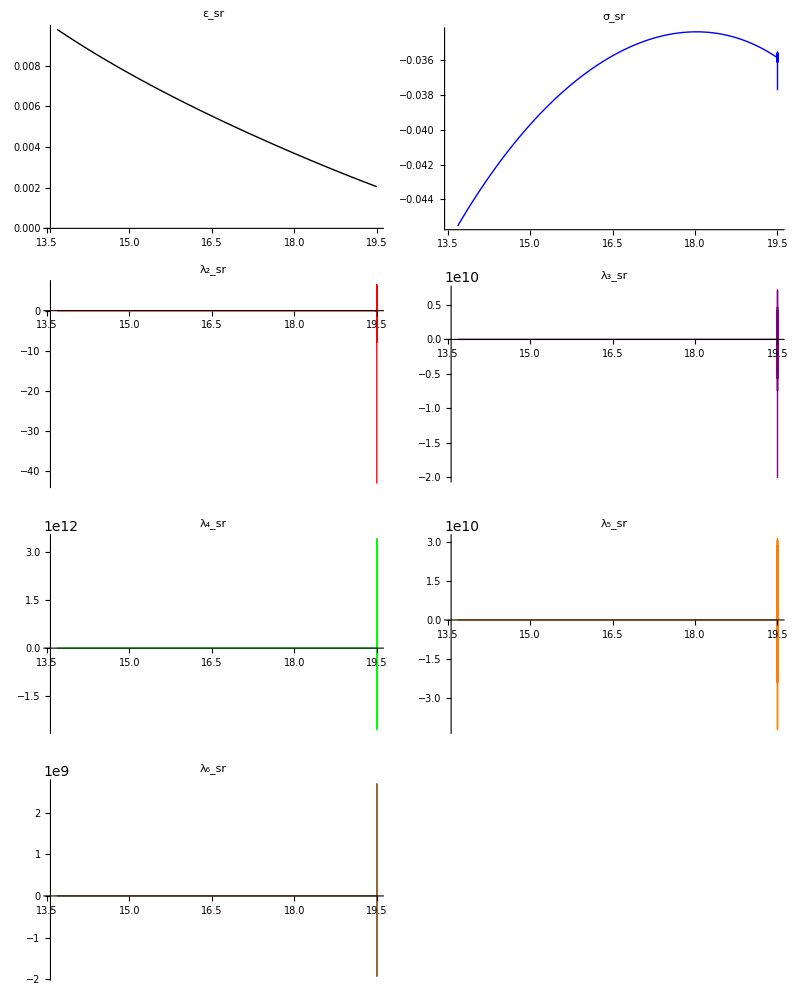

```mathematica
ϕinf=ϕvals;
Vinf=Vvals;
Hinf=Hvals;
Ninf=Nvals-Min[Nvals];
epsinf=epsvals;

MinMax[ϕinf]
epsPhidef = εsr /@ ϕinf;
MinMax[epsPhidef]
sigPhidef = σsr /@ ϕinf;
lam2srPhidef = λ2sr /@ ϕinf;
lam3srPhidef = λ3sr /@ ϕinf;
lam4srPhidef = λ4sr /@ ϕinf;
lam5srPhidef = λ5sr /@ ϕinf;
lam6srPhidef = λ6sr /@ ϕinf;

pEps=ListLinePlot[Transpose[{ϕinf,epsPhidef}],PlotLabel->"ε_sr",PlotStyle->{Thick,Black},PlotRange->All];

pSig=ListLinePlot[Transpose[{ϕinf,sigPhidef}],PlotLabel->"σ_sr",PlotStyle->{Thick,Blue},PlotRange->All];

pLam2=ListLinePlot[Transpose[{ϕinf,lam2srPhidef}],PlotLabel->"λ₂_sr",PlotStyle->{Thick,Red},PlotRange->All];

pLam3=ListLinePlot[Transpose[{ϕinf,lam3srPhidef}],PlotLabel->"λ₃_sr",PlotStyle->{Thick,Purple},PlotRange->All];

pLam4=ListLinePlot[Transpose[{ϕinf,lam4srPhidef}],PlotLabel->"λ₄_sr",PlotStyle->{Thick,Green},PlotRange->All];

pLam5=ListLinePlot[Transpose[{ϕinf,lam5srPhidef}],PlotLabel->"λ₅_sr",PlotStyle->{Thick,Orange},PlotRange->All];

pLam6=ListLinePlot[Transpose[{ϕinf,lam6srPhidef}],PlotLabel->"λ₆_sr",PlotStyle->{Thick,Brown},PlotRange->All];

GraphicsGrid[{{pEps,pSig},{pLam2,pLam3},{pLam4,pLam5},{pLam6,Null}},Spacings->{2,2}]
```

```mathematica
phiOfNInterpsr=Interpolation[Transpose[{Ninf,ϕinf}],InterpolationOrder->3]; (*only difference is changing the interp order*)
phiOfNsr[n_]:=phiOfNInterpsr[n];
εsrOfN[n_]:=εsr[phiOfNsr[n]];
σsrOfN[n_]:=σsr[phiOfNsr[n]];
λ2srOfN[n_]:=λ2sr[phiOfNsr[n]];

depsdNsr[n_]:=εsrOfN'[n]
dsigmadNsr[n_]:=σsrOfN'[n]
dlam2dNsr[n_]:=λ2srOfN'[n]

(*I am using flow equations for the rest*)
λ3OfNsr[n_]:=dlam2dNsr[n]-(1/2) σsrOfN[n]*λ2srOfN[n]
dlam3dNsr[n_]:=λ3OfNsr'[n];

λ4OfNsr[n_]:=dlam3dNsr[n]-(σsrOfN[n]* λ3OfNsr[n])-(εsrOfN[n]* λ3OfNsr[n]);
dlam4dNsr[n_]:=λ4OfNsr'[n];

λ5OfNsr[n_]:=dlam4dNsr[n]-((3/2 )* σsrOfN[n]* λ4OfNsr[n])-(2 *εsrOfN[n]* λ4OfNsr[n]) ;
dlam5dNsr[n_]:=λ5OfNsr'[n];
(*dlam5dNdyn[n_]:=Derivative[1][λ5OfNdyn][n];*)

λ6OfNsr[n_]:=dlam5dNsr[n]-(2* σsrOfN[n]* λ5OfNsr[n])-(3 *εsrOfN[n]* λ5OfNsr[n]);
```

```mathematica
epssrN = εsrOfN[Ninf];
sigsrN = σsrOfN[Ninf];
lam2srN = λ2srOfN[Ninf];
lam3srN = λ3OfNsr[Ninf];
lam4srN = λ4OfNsr[Ninf];
lam5srN = λ5OfNsr[Ninf];
lam6srN = λ6OfNsr[Ninf];
```

Out of curiosity, I want to check something: How different is H_inf from√(V_inf/3). This is done later in the notebook.

### Test 2: The Mid-Flow Interpolation Method uses the directly calculated H(ϕ) from our imports to build a spline for ε (ϕ) = ε_dyn

Now, one comparison we can make is the comparison between different methods of acquiring ε(ϕ) where we use the more dynamical ε with the mask applied to it from our data. In other words ε_sr (symbolic) is fully from the definition of the potential that has been interpolated and plugged into H_sr which we approximate to be the square root of that interpolated potential (V)/3. Derivatives of H_sr are used to find the this symbolic ε_sr. This compares to the original ε which I will call the dynamic form where we make an interpolated function of H from the data and then apply an inflationary mask cut off that obeys ε < 1 . We’ll discuss the third method which will explicitly use flow equations in the Test 3 section. 

I can also fully use the ε_dyn I have here to find all of the slow roll parameters as a function of N. Initially, the method I used to find the SRPs required me to define ϕ(N) which I then plugged into the expressions below. Note, the first three parameters will use interpolation methods made from the data .

```mathematica
HInterpinf=Interpolation[Transpose[{ϕinf,Hinf}],InterpolationOrder->4]

dHphidyn[ϕ_]:=HInterpinf'[ϕ];
dH2phidyn[ϕ_]:=HInterpinf''[ϕ];
dH3phidyn[ϕ_]:=Derivative[3][HInterpinf][ϕ];
dH4phidyn[ϕ_]:=Derivative[4][HInterpinf][ϕ];
dH5phidyn[ϕ_]:=Derivative[5][HInterpinf][ϕ];
dH6phidyn[ϕ_]:=Derivative[6][HInterpinf][ϕ];
dH7phidyn[ϕ_]:=Derivative[7][HInterpinf][ϕ];
dH8phidyn[ϕ_]:=Derivative[8][HInterpinf][ϕ];
```

InterpolatingFunction[…]

```mathematica
(*Slow Roll Parameters*)
εdyn[ϕ_]:=2 (dHphidyn[ϕ]/HInterpinf[ϕ])^2;
σdyn[ϕ_]:=8*((dH2phidyn[ϕ]/(2*HInterpinf[ϕ]))-(dHphidyn[ϕ]/HInterpinf[ϕ])^2);
(*Higher-order slow-roll parameters*)
λ2dyn[ϕ_]:=2^2*(dHphidyn[ϕ]/HInterpinf[ϕ]^2)* dH3phidyn[ϕ];
λ3dyn[ϕ_]:=2^3*(dHphidyn[ϕ]/HInterpinf[ϕ])^2*dH4phidyn[ϕ]/HInterpinf[ϕ]^3; (*Again, only use up to lam2*)
λ4dyn[ϕ_]:=2^4*(dHphidyn[ϕ])^3*(dH5phidyn[ϕ])/HInterpinf[ϕ]^5;
λ5dyn[ϕ_]:=2^5*(dHphidyn[ϕ])^4*(dH6phidyn[ϕ])/HInterpinf[ϕ]^6;
λ6dyn[ϕ_]:=2^6*(dHphidyn[ϕ])^5*(dH7phidyn[ϕ])/HInterpinf[ϕ]^7;
```

```mathematica
phiOfNInterpdyn=Interpolation[Transpose[{Ninf,ϕinf}],InterpolationOrder->3]; (*only difference is changing the interp order*)
phiOfNdyn[n_]:=phiOfNInterpdyn[n];
εdynOfN[n_]:=εdyn[phiOfNdyn[n]];
σdynOfN[n_]:=σdyn[phiOfNdyn[n]];
λ2dynOfN[n_]:=λ2dyn[phiOfNdyn[n]];

depsdNdyn[n_]:=εdynOfN'[n]
dsigmadNdyn[n_]:=σdynOfN'[n]
dlam2dNdyn[n_]:=λ2dynOfN'[n]

(*I am using flow equations for the rest*)
λ3OfNdyn[n_]:=dlam2dNdyn[n]-(1/2) σdynOfN[n]*λ2dynOfN[n]
dlam3dNdyn[n_]:=λ3OfNdyn'[n];

λ4OfNdyn[n_]:=dlam3dNdyn[n]-(σdynOfN[n]* λ3OfNdyn[n])-(εdynOfN[n]* λ3OfNdyn[n]);
dlam4dNdyn[n_]:=λ4OfNdyn'[n];

λ5OfNdyn[n_]:=dlam4dNdyn[n]-((3/2 )* σdynOfN[n]* λ4OfNdyn[n])-(2 *εdynOfN[n]* λ4OfNdyn[n]) ;
dlam5dNdyn[n_]:=λ5OfNdyn'[n];
(*dlam5dNdyn[n_]:=Derivative[1][λ5OfNdyn][n];*)

λ6OfNdyn[n_]:=dlam5dNdyn[n]-(2* σdynOfN[n]* λ5OfNdyn[n])-(3 *εdynOfN[n]* λ5OfNdyn[n]);
```

{13.6835,19.5}

{0.00204943,0.00970918}

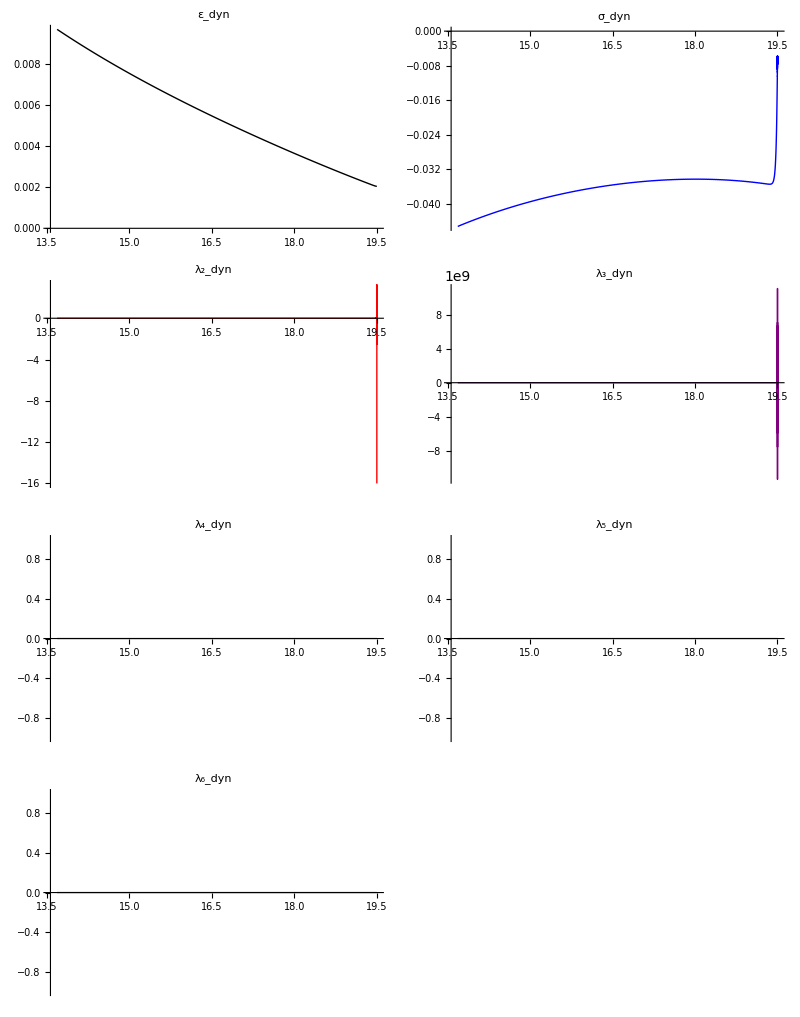

```mathematica
MinMax[ϕinf]
epsPhidyn= εdyn /@ ϕinf;
MinMax[epsPhidyn]
sigPhidyn = σdyn /@ ϕinf;
lam2srPhidyn = λ2dyn /@ ϕinf;
lam3srPhidyn = λ3dyn /@ ϕinf;
lam4srPhidyn = λ4dyn /@ ϕinf;
lam5srPhidyn = λ5dyn /@ ϕinf;
lam6srPhidyn = λ6dyn /@ ϕinf;

pEpsdyn=ListLinePlot[Transpose[{ϕinf,epsPhidyn}],PlotLabel->"ε_dyn",PlotStyle->{Thick,Black},PlotRange->All];

pSigdyn=ListLinePlot[Transpose[{ϕinf,sigPhidyn}],PlotLabel->"σ_dyn",PlotStyle->{Thick,Blue},PlotRange->All];

pLam2dyn=ListLinePlot[Transpose[{ϕinf,lam2srPhidyn}],PlotLabel->"λ₂_dyn",PlotStyle->{Thick,Red},PlotRange->All];

pLam3dyn=ListLinePlot[Transpose[{ϕinf,lam3srPhidyn}],PlotLabel->"λ₃_dyn",PlotStyle->{Thick,Purple},PlotRange->All];

pLam4dyn=ListLinePlot[Transpose[{ϕinf,lam4srPhidyn}],PlotLabel->"λ₄_dyn",PlotStyle->{Thick,Green},PlotRange->All];

pLam5dyn=ListLinePlot[Transpose[{ϕinf,lam5srPhidyn}],PlotLabel->"λ₅_dyn",PlotStyle->{Thick,Orange},PlotRange->All];

pLam6dyn=ListLinePlot[Transpose[{ϕinf,lam6srPhidyn}],PlotLabel->"λ₆_dyn",PlotStyle->{Thick,Brown},PlotRange->All];

GraphicsGrid[{{pEpsdyn,pSigdyn},{pLam2dyn,pLam3dyn},{pLam4dyn,pLam5dyn},{pLam6dyn,Null}},Spacings->{2,2}]
```

### Test 3: Full Flow -- Meaning I redefine ε (ϕ) using the full flow definitions using H_inf (N_inf)

The third method I am shooting for won’t use ϕ(N) in the calculation at all and instead will only use the flow equations which again can be found in this paper. I only bring out ϕ(N) so I can later compare it to Tests 1 & 2 which require ε(ϕ).

```mathematica
HInterpN=Interpolation[Transpose[{Ninf,Hinf}],InterpolationOrder->3]
(*HNvals=HInterpN/@Ninf;*)

dHN[N_]:=HInterpN'[N];
(*dHNvals=(HInterpN')/@Ninf;*)

εflow[N_]:=(dHN[N]/HInterpN[N]);
(*εflow=dHNvals/HNvals;*)
(*dεflowdN[N_]:=εflow'[N];*)
dεflowdN[N_]:=Derivative[1][εflow][N];
σflow[N_]:=(dεflowdN[N]/εflow[N])-2*εflow[N];
dσflowdN[N_]:= Derivative[1][σflow][N];
λ2flow[N_]:=(5/2*εflow[N]*σflow[N]) + 6*(εflow[N]^2) - dσflowdN[N];
dλ2flowdN[N_]:= Derivative[1][λ2flow][N];

(*I am using flow equations for the rest*)
λ3flow[N_]:=dλ2flowdN[N]-(1/2* σflow[N] λ2flow[N]);
dλ3flowdN[N_]:=Derivative[1][λ3flow][N];

λ4flow[N_]:=dλ3flowdN[N]-(σflow[N]* λ3flow[N])-(εflow[N]* λ3flow[N]);
dλ4flowdN[N_]:=Derivative[1][λ4flow][N];

λ5flow[N_]:=dλ4flowdN[N]-(3/2 * σflow[N]*λ4flow[N])-(2 *εflow[N]* λ4flow[N]);
dλ5flowdN[N_]:=Derivative[1][λ5flow][N];

λ6flow[N_]:=dλ5flowdN[N]-(2 *σflow[N]*λ5flow[N])-(3 *εflow[N]* λ5flow[N]);
```

InterpolatingFunction[…]

Now, let’s apply it:

```mathematica
MinMax[Ninf]
epsflow= εflow /@ Ninf;
MinMax[epsflow]
sigflow = σflow /@ Ninf;
lam2flow = λ2flow /@ Ninf;
lam3flow = λ3flow /@ Ninf;
lam4flow = λ4flow /@ Ninf;
lam5flow = λ5flow /@ Ninf;
lam6flow= λ6flow /@ Ninf;
```

{0.,59.2284}

{0.00204943,0.00970918}

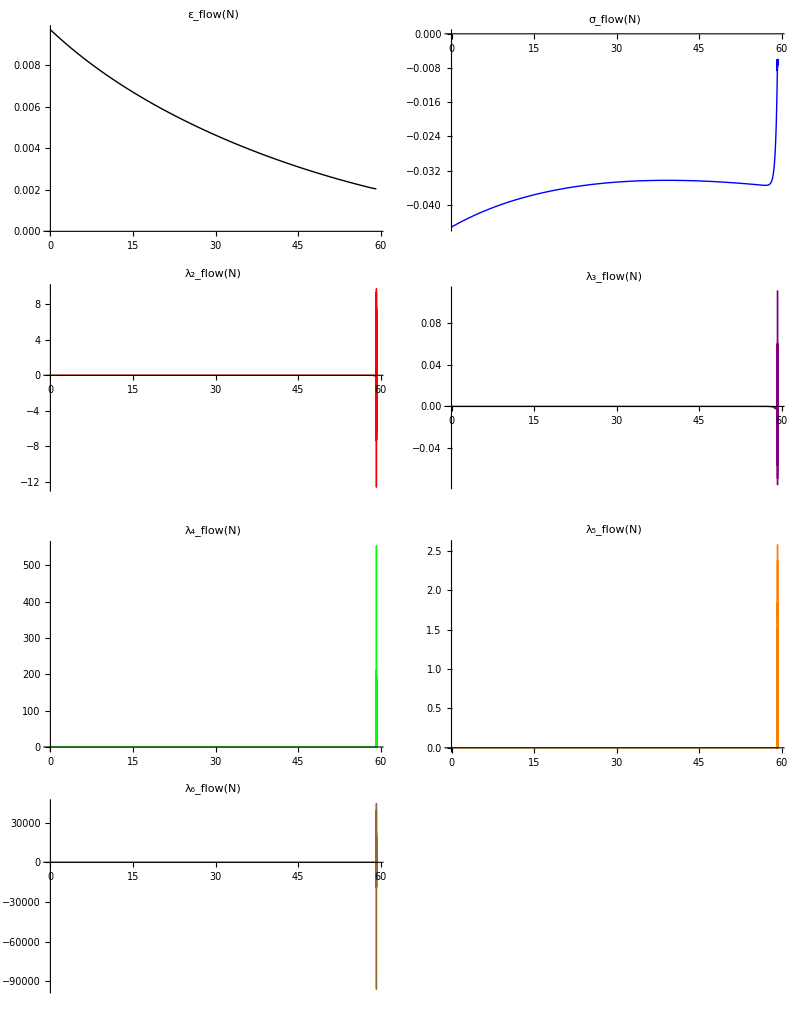

```mathematica
pEpsflow=ListLinePlot[Transpose[{Ninf,epsflow}],PlotLabel->"ε_flow(N)",PlotStyle->{Thick,Black},PlotRange->All];

pSigflow=ListLinePlot[Transpose[{Ninf,sigflow}],PlotLabel->"σ_flow(N)",PlotStyle->{Thick,Blue},PlotRange->All];

pLam2flow=ListLinePlot[Transpose[{Ninf,lam2flow}],PlotLabel->"λ₂_flow(N)",PlotStyle->{Thick,Red},PlotRange->All];

pLam3flow=ListLinePlot[Transpose[{Ninf,lam3flow}],PlotLabel->"λ₃_flow(N)",PlotStyle->{Thick,Purple},PlotRange->All];

pLam4flow=ListLinePlot[Transpose[{Ninf,lam4flow}],PlotLabel->"λ₄_flow(N)",PlotStyle->{Thick,Green},PlotRange->All];

pLam5flow=ListLinePlot[Transpose[{Ninf,lam5flow}],PlotLabel->"λ₅_flow(N)",PlotStyle->{Thick,Orange},PlotRange->All];

pLam6flow=ListLinePlot[Transpose[{Ninf,lam6flow}],PlotLabel->"λ₆_flow(N)",PlotStyle->{Thick,Brown},PlotRange->All];

GraphicsGrid[{{pEpsflow,pSigflow},{pLam2flow,pLam3flow},{pLam4flow,pLam5flow},{pLam6flow,Null}},Spacings->{2,2}]
```

Above was as a function of N, let’s put it in the form of ε(ϕ):

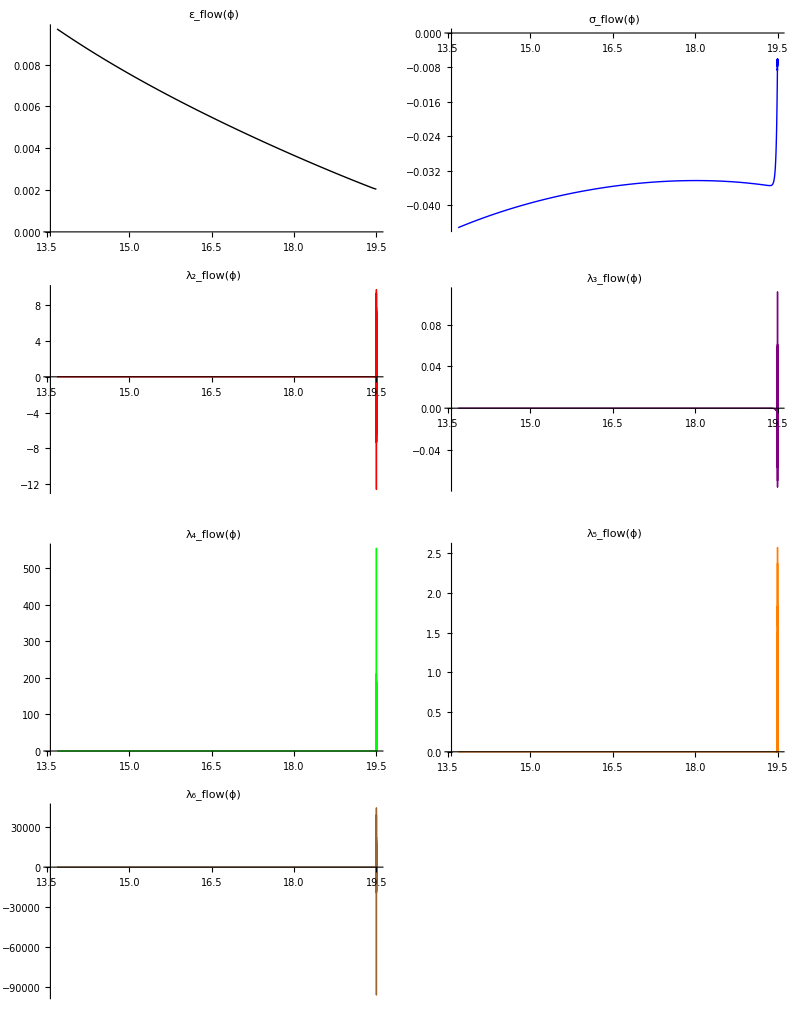

```mathematica
(*We used the definition below earlier in test 2 which gives us ϕ(N)*)
(*phiOfNInterpdyn=Interpolation[Transpose[{Ninf,ϕinf}],InterpolationOrder->5]; (*only difference is changing the interp order*)
phiOfNdyn[n_]:=phiOfNInterpdyn[n];*)

epsflowPhi=Transpose[{phiOfNdyn/@Ninf,epsflow}];
sigflowPhi=Transpose[{phiOfNdyn/@Ninf,sigflow}];
lam2flowPhi=Transpose[{phiOfNdyn/@Ninf,lam2flow}];
lam3flowPhi=Transpose[{phiOfNdyn/@Ninf,lam3flow}];
lam4flowPhi=Transpose[{phiOfNdyn/@Ninf,lam4flow}];
lam5flowPhi=Transpose[{phiOfNdyn/@Ninf,lam5flow}];
lam6flowPhi=Transpose[{phiOfNdyn/@Ninf,lam6flow}];

(*epsflowInterpPhi=Interpolation[epsflowPhi,InterpolationOrder->3];
sigflowInterpPhi=Interpolation[sigflowPhi,InterpolationOrder->3];
lam2flowInterpPhi=Interpolation[lam2flowPhi,InterpolationOrder->3];
lam3flowInterpPhi=Interpolation[lam3flowPhi,InterpolationOrder->3];
lam4flowInterpPhi=Interpolation[lam4flowPhi,InterpolationOrder->3];
lam5flowInterpPhi=Interpolation[lam5flowPhi,InterpolationOrder->3];
lam6flowInterpPhi=Interpolation[lam6flowPhi,InterpolationOrder->3];*)

pEpsflowphi=ListLinePlot[epsflowPhi,PlotLabel->"ε_flow(ϕ)",PlotStyle->{Thick,Black},PlotRange->All];
pSigflowphi=ListLinePlot[sigflowPhi,PlotLabel->"σ_flow(ϕ)",PlotStyle->{Thick,Blue},PlotRange->All];
pLam2flowphi=ListLinePlot[lam2flowPhi,PlotLabel->"λ₂_flow(ϕ)",PlotStyle->{Thick,Red},PlotRange->All];
pLam3flowphi=ListLinePlot[lam3flowPhi,PlotLabel->"λ₃_flow(ϕ)",PlotStyle->{Thick,Purple},PlotRange->All];
pLam4flowphi=ListLinePlot[lam4flowPhi,PlotLabel->"λ₄_flow(ϕ)",PlotStyle->{Thick,Green},PlotRange->All];
pLam5flowphi=ListLinePlot[lam5flowPhi,PlotLabel->"λ₅_flow(ϕ)",PlotStyle->{Thick,Orange},PlotRange->All];
pLam6flowphi=ListLinePlot[lam6flowPhi,PlotLabel->"λ₆_flow(ϕ)",PlotStyle->{Thick,Brown},PlotRange->All];

GraphicsGrid[{{pEpsflowphi,pSigflowphi},{pLam2flowphi,pLam3flowphi},{pLam4flowphi,pLam5flowphi},{pLam6flowphi,Null}},Spacings->{2,2}]
```

### Comparison of H_sr, H_dyn, H_flow

InterpolatingFunction[…]

H_sr Min , Max = {5.54699×10^-3,7.49189×10^-3}

H_dyn Min , Max = {5.55598×10^-3,7.49445×10^-3}

H_flow Min , Max = {5.55598×10^-3,7.49445×10^-3}

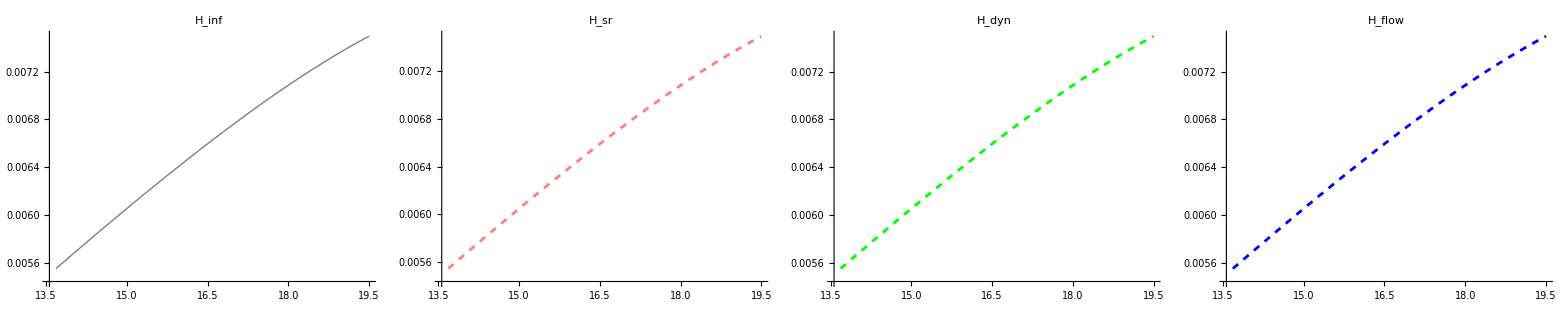

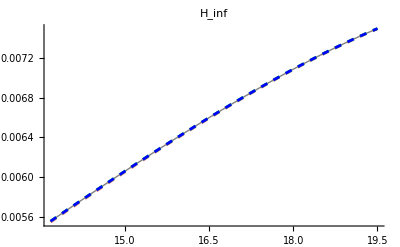

```mathematica
Hinftest=ListLinePlot[Transpose[{ϕinf,Hinf}],PlotLabel->"H_inf",PlotStyle->{Thick,Gray},PlotRange->All];

HPhidyn= HInterpinf /@ ϕinf;
Hdyntest = ListLinePlot[Transpose[{ϕinf,HPhidyn}],PlotLabel->"H_dyn",PlotStyle->{Dashed,Green},PlotRange->All];

Hsrvals=Sqrt[Vinf/3];
Hsrtest = ListLinePlot[Transpose[{ϕinf,Hsrvals}],PlotLabel->"H_sr",PlotStyle->{Dashed,Pink},PlotRange->All];

HNflow = Interpolation[Transpose[{Ninf,Hinf}],InterpolationOrder->5]
Hflow = Transpose[{phiOfNdyn/@Ninf,HNflow/@Ninf}]
Hflowtest=ListLinePlot[Hflow,PlotLabel->"H_flow",PlotStyle->{Dashed,Blue},PlotRange->All];

(*HAnalytictest = ListLinePlot[Transpose[{ϕinf,HAnalyticInf}],PlotLabel->"H_Analytic",PlotStyle->{Dashed,Pink},PlotRange->All];*)

Print["H_sr Min , Max = ",MinMax[Hsrvals]//ScientificForm];
Print[(*"H_Analytic Min , Max = ",MinMax[HAnalyticInf]//ScientificForm*)];
Print["H_dyn Min , Max = ",MinMax[HPhidyn]//ScientificForm];
Print["H_flow Min , Max = ",MinMax[Last/@Hflow]//ScientificForm]

(*GraphicsGrid[{{Hinftest,Hsrtest, Hdyntest, Hflowtest,HAnalytictest}},Spacings->{2,2}]*)
GraphicsGrid[{{Hinftest,Hsrtest, Hdyntest, Hflowtest}},Spacings->{2,2}]

Show[Hinftest,Hsrtest,Hdyntest,Hflowtest,PlotRange->All]
(*ListLinePlot[{Transpose[{ϕinf,Hinf}],Transpose[{ϕinf,Hsrtest}]},PlotLegends->{"H_inf (data-driven)","H_sr (symbolic)"},PlotRange->All,PlotStyle->{Thick,Dashed}]*)
```

### Comparison of ε_sr, ε_dyn, ε_flow

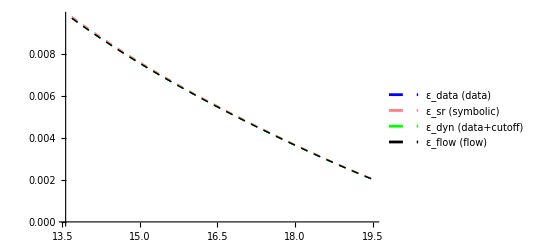

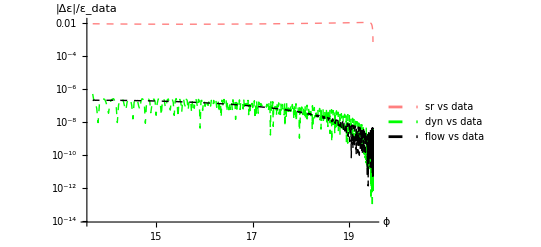

```mathematica
epsPlots = {Transpose[{ϕinf,epsinf}],Transpose[{ϕinf,epsPhidef}], Transpose[{ϕinf,epsPhidyn}], Transpose[{phiOfNdyn/@Ninf,epsflow}]}
ListLinePlot[epsPlots,PlotLegends->{"ε_data (data)","ε_sr (symbolic)", "ε_dyn (data+cutoff)", "ε_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Blue},{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None,None}]

relDiffsr=Abs[(epsPhidef-epsinf)/epsinf];
relDiffdyn=Abs[(epsPhidyn-epsinf)/epsinf];

epsflowVals=epsflowPhi[[All,2]];(*pull out epsilon column*)
relDiffflow=Abs[(epsflowVals-epsinf)/epsinf];

relDiffPlots={Transpose[{ϕinf,relDiffsr}],Transpose[{ϕinf,relDiffdyn}],Transpose[{ϕinf,relDiffflow}]};

ListLinePlot[relDiffPlots,PlotLegends->{"sr vs data","dyn vs data","flow vs data"},AxesLabel->{"ϕ","|Δε|/ε_data"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}}]
```

As you can see the symbolic form of ε matches well at high field values but they have a discrepancy the more the field rolls down as ϕ → 0.

We should now consider looking at the higher order parameters to see how they differ from one another.

### Comparison of σ_sr, σ_dyn, σ_flow

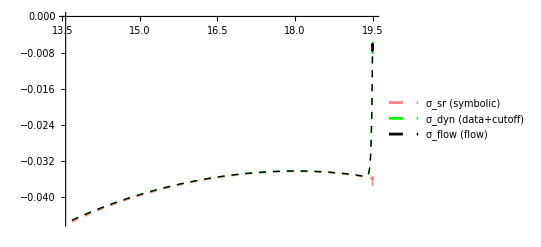

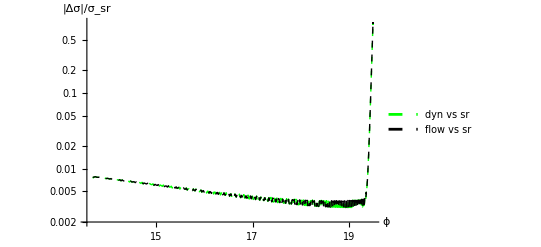

```mathematica
sigPlots = {Transpose[{ϕinf,sigPhidef}], Transpose[{ϕinf,sigPhidyn}], Transpose[{phiOfNdyn/@Ninf,sigflow}]}
ListLinePlot[sigPlots,PlotLegends->{"σ_sr (symbolic)", "σ_dyn (data+cutoff)", "σ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}]

sigrelDiffdyn=Abs[(sigPhidyn-sigPhidef)/sigPhidef];
sigflowVals=sigflowPhi[[All,2]];(*pull out sig column*)
sigrelDiffflow=Abs[(sigflowVals-sigPhidef)/sigPhidef];

sigrelDiffPlots={Transpose[{ϕinf,sigrelDiffdyn}],Transpose[{ϕinf,sigrelDiffflow}]};

ListLinePlot[sigrelDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δσ|/σ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}]
```

### Comparison of ^2 λ_sr, (^2 λ_sr)_dyn, (^2 λ_sr)_flow

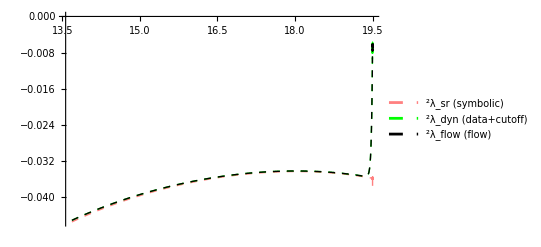

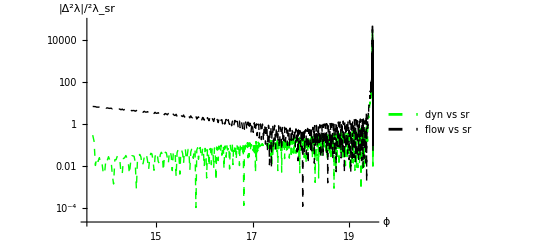

```mathematica
lam2Plots = {Transpose[{ϕinf,lam2srPhidef}], Transpose[{ϕinf,lam2srPhidyn}], Transpose[{phiOfNdyn/@Ninf,lam2flow}]}
ListLinePlot[sigPlots,PlotLegends->{"^2λ_sr (symbolic)", "^2λ_dyn (data+cutoff)", "^2λ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}]

lam2relDiffdyn=Abs[(lam2srPhidyn-lam2srPhidef)/lam2srPhidef];
lam2flowVals=lam2flowPhi[[All,2]];(*pull out sig column*)
lam2relDiffflow=Abs[(lam2flowVals-lam2srPhidef)/lam2srPhidef];

lam2relDiffPlots={Transpose[{ϕinf,lam2relDiffdyn}],Transpose[{ϕinf,lam2relDiffflow}]};

ListLinePlot[lam2relDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δ^2λ|/^2λ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}]
```

### Comparing All SRPs for Dynamic and Flow to Hubble Slow-Roll

```mathematica
(*epsilon*)

epsPlots = {Transpose[{ϕinf,epsinf}],Transpose[{ϕinf,epsPhidef}], Transpose[{ϕinf,epsPhidyn}], Transpose[{phiOfNdyn/@Ninf,epsflow}]};
compeps = ListLinePlot[epsPlots,PlotLegends->{"ε_data (data)","ε_sr (symbolic)", "ε_dyn (data+cutoff)", "ε_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Blue},{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None,None}];

(*relDiffsr=Abs[(epsPhidef-epsinf)/epsinf];*)
relDiffdynsr=Abs[(epsPhidyn-epsPhidef)/epsPhidef];

epsflowVals=epsflowPhi[[All,2]];(*pull out epsilon column*)
relDiffflowsr=Abs[(epsflowVals-epsPhidef)/epsPhidef];

relDiffPlotssr={Transpose[{ϕinf,relDiffdynsr}],Transpose[{ϕinf,relDiffflowsr}]};

compreleps =ListLinePlot[relDiffPlotssr,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δε|/ε_data"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}];


(*sigma*)
sigPlots = {Transpose[{ϕinf,sigPhidef}], Transpose[{ϕinf,sigPhidyn}], Transpose[{phiOfNdyn/@Ninf,sigflow}]};
compsig = ListLinePlot[sigPlots,PlotLegends->{"σ_sr (symbolic)", "σ_dyn (data+cutoff)", "σ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}];

sigrelDiffdyn=Abs[(sigPhidyn-sigPhidef)/sigPhidef];
sigflowVals=sigflowPhi[[All,2]];(*pull out sig column*)
sigrelDiffflow=Abs[(sigflowVals-sigPhidef)/sigPhidef];

sigrelDiffPlots={Transpose[{ϕinf,sigrelDiffdyn}],Transpose[{ϕinf,sigrelDiffflow}]};

comprelsig = ListLinePlot[sigrelDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δσ|/σ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}];

(*lambda2*)
lam2Plots = {Transpose[{ϕinf,lam2srPhidef}], Transpose[{ϕinf,lam2srPhidyn}], Transpose[{phiOfNdyn/@Ninf,lam2flow}]};
complam2 = ListLinePlot[lam2Plots,PlotLegends->{"^2λ_sr (symbolic)", "^2λ_dyn (data+cutoff)", "^2λ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}];

lam2relDiffdyn=Abs[(lam2srPhidyn-lam2srPhidef)/lam2srPhidef];
lam2flowVals=lam2flowPhi[[All,2]];(*pull out sig column*)
lam2relDiffflow=Abs[(lam2flowVals-lam2srPhidef)/lam2srPhidef];

lam2relDiffPlots={Transpose[{ϕinf,lam2relDiffdyn}],Transpose[{ϕinf,lam2relDiffflow}]};

comprellam2 =ListLinePlot[lam2relDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δ^2λ|/^2λ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}];

(*lambda3*)
lam3Plots = {Transpose[{ϕinf,lam3srPhidef}], Transpose[{ϕinf,lam3srPhidyn}], Transpose[{phiOfNdyn/@Ninf,lam3flow}]};
complam3 = ListLinePlot[lam3Plots,PlotLegends->{"^3λ_sr (symbolic)", "^3λ_dyn (data+cutoff)", "^3λ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}];

lam3relDiffdyn=Abs[(lam3srPhidyn-lam3srPhidef)/lam3srPhidef];
lam3flowVals=lam3flowPhi[[All,2]];(*pull out sig column*)
lam3relDiffflow=Abs[(lam3flowVals-lam3srPhidef)/lam3srPhidef];

lam3relDiffPlots={Transpose[{ϕinf,lam3relDiffdyn}],Transpose[{ϕinf,lam3relDiffflow}]};

comprellam3 =ListLinePlot[lam3relDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δ^3λ|/^3λ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}];

(*lambda4*)
lam4Plots = {Transpose[{ϕinf,lam4srPhidef}], Transpose[{ϕinf,lam4srPhidyn}], Transpose[{phiOfNdyn/@Ninf,lam4flow}]};
complam4 = ListLinePlot[lam4Plots,PlotLegends->{"^4λ_sr (symbolic)", "^4λ_dyn (data+cutoff)", "^4λ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}];

lam4relDiffdyn=Abs[(lam4srPhidyn-lam4srPhidef)/lam4srPhidef];
lam4flowVals=lam4flowPhi[[All,2]];(*pull out sig column*)
lam4relDiffflow=Abs[(lam4flowVals-lam4srPhidef)/lam4srPhidef];

lam4relDiffPlots={Transpose[{ϕinf,lam4relDiffdyn}],Transpose[{ϕinf,lam4relDiffflow}]};

comprellam4 =ListLinePlot[lam4relDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δ^4λ|/^4λ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}];

(*lambda5*)
lam5Plots = {Transpose[{ϕinf,lam5srPhidef}], Transpose[{ϕinf,lam5srPhidyn}], Transpose[{phiOfNdyn/@Ninf,lam5flow}]};
complam5 = ListLinePlot[lam5Plots,PlotLegends->{"^5λ_sr (symbolic)", "^5λ_dyn (data+cutoff)", "^5λ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}];

lam5relDiffdyn=Abs[(lam5srPhidyn-lam5srPhidef)/lam5srPhidef];
lam5flowVals=lam5flowPhi[[All,2]];(*pull out sig column*)
lam5relDiffflow=Abs[(lam5flowVals-lam5srPhidef)/lam5srPhidef];

lam5relDiffPlots={Transpose[{ϕinf,lam5relDiffdyn}],Transpose[{ϕinf,lam5relDiffflow}]};

comprellam5 =ListLinePlot[lam5relDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δ^5λ|/^5λ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}];

(*lambda6*)
lam6Plots = {Transpose[{ϕinf,lam6srPhidef}], Transpose[{ϕinf,lam6srPhidyn}], Transpose[{phiOfNdyn/@Ninf,lam6flow}]};
complam6 = ListLinePlot[lam6Plots,PlotLegends->{"^6λ_sr (symbolic)", "^6λ_dyn (data+cutoff)", "^6λ_flow (flow)"},PlotRange->All,PlotStyle->{{Thick,Dashed,Pink},{Thick,Dashed,Green},{Thick,Dashed,Black}},PlotMarkers->{None,None,None}];

lam6relDiffdyn=Abs[(lam6srPhidyn-lam6srPhidef)/lam6srPhidef];
lam6flowVals=lam6flowPhi[[All,2]];(*pull out sig column*)
lam6relDiffflow=Abs[(lam6flowVals-lam6srPhidef)/lam6srPhidef];

lam6relDiffPlots={Transpose[{ϕinf,lam6relDiffdyn}],Transpose[{ϕinf,lam6relDiffflow}]};

comprellam6 =ListLinePlot[lam6relDiffPlots,PlotLegends->{"dyn vs sr","flow vs sr"},AxesLabel->{"ϕ","|Δ^6λ|/^6λ_sr"},PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->{{Thick,Dashed,Green},{Thick,Dashed,Black}}];

GraphicsGrid[{{compeps,compsig,complam2},{complam3,complam4,complam5},{complam6,Null,Null}},Spacings->{3,3},ImageSize->1500 ]

GraphicsGrid[{{compreleps,comprelsig,comprellam2},{comprellam3,comprellam4,comprellam5},{comprellam6,Null,Null}},Spacings->{3,3},ImageSize->1500]

(*GraphicsGrid[{{compeps,compsig,complam2,complam3,complam4,complam5,complam6},{compreleps,comprelsig,comprellam2,comprellam3,comprellam4,comprellam5,comprellam6}},Spacings->{2,2}]*)

(*GraphicsGrid[{{compeps,compsig,complam2,complam3,complam4,complam5,complam6}},Spacings->{2,2}]
GraphicsGrid[{{compreleps,comprelsig,comprellam2,comprellam3,comprellam4,comprellam5,comprellam6}},Spacings->{2,2}]*)
```

-Graphics-

-Graphics-

### Comparing Observables for Methods

Each of these methods will produce values of SRPs that I would expect to be marginally different. Below I will present a table for each case which can be used to compare  with the other expected slow roll parameters at the pivot N (desired number of e-folds). Our constant are defined below for all cases:

```mathematica
(*In all cases*)
(*Constant C*)γ=0.5772156649;
Const=4 (Log[2]+γ)-5;

(*Pivot point or Nstar*)
(*Npiv=Max[Ninf]-1*)
Npiv = 58
```

58

```mathematica
(*HUBBLE SLOW ROLL EXPECTED OBSERVABLES*)
εpivsr=εsrOfN[Npiv];
σpivsr=σsrOfN[Npiv];
λ2pivsr=λ2srOfN[Npiv];
λ3pivsr=λ3OfNsr[Npiv];
λ4pivsr=λ4OfNsr[Npiv];
λ5pivsr=λ5OfNsr[Npiv];
λ6pivsr=λ6OfNsr[Npiv];

(*We need derivatives at Npiv*)
dεpivsr= depsdNsr[Npiv];
dσpivsr=dsigmadNsr[Npiv];
dλ2pivsr=dlam2dNsr[Npiv];

rhighsr = 16*εpivsr*(1-Const*(σpivsr+2*εpivsr));
rlowsr = 16*εpivsr;
nshighsr = 1+σpivsr-((5-(3*Const))*εpivsr^2)-(0.25*(3-(5*Const))*σpivsr*εpivsr)+(0.5*(3-Const)*λ2pivsr);
nslowsr= σpivsr+1;

(*Need the dns/dN parameter for the running spectral index*)
dnsdNsr = (dσpivsr-2*(5-(3*Const))*εpivsr*dεpivsr-0.25*(3-(5*Const))*(dσpivsr*εpivsr+σpivsr*dεpivsr)+0.5*(3-Const)*dλ2pivsr);
alphahighsr= -(1/(1-εpivsr))*dnsdNsr;
alphalowsr= 0;

Grid[{{"ε(N="<>ToString[Npiv]<>")",εpivsr},{"σ(N="<>ToString[Npiv]<>")",σpivsr},{"λ₂(N="<>ToString[Npiv]<>")",λ2pivsr},{"λ₃(N="<>ToString[Npiv]<>")",λ3pivsr},{"λ₄(N="<>ToString[Npiv]<>")",λ4pivsr},{"λ₅(N="<>ToString[Npiv]<>")",λ5pivsr},{"λ₆(N="<>ToString[Npiv]<>")",λ6pivsr},{"r (low)",rlowsr},{"r (high)",rhighsr},{"nₛ (low)",nslowsr},{"nₛ (high)",nshighsr},{"αₛ (low)",alphalowsr},{"αₛ (high)",alphahighsr}},Frame->All,Alignment->Left,Background->{None,{{LightGray,White}}}]
```

ε(N=58) | 0.00213166
σ(N=58) | -0.0356948
λ₂(N=58) | -0.000228347
λ₃(N=58) | 0.000190155
λ₄(N=58) | 0.0337111
λ₅(N=58) | -0.000378739
λ₆(N=58) | 0.000172465
r (low) | 0.0341065
r (high) | 0.0341939
nₛ (low) | 0.964305
nₛ (high) | 0.964
αₛ (low) | 0
αₛ (high) | -0.00015364

```mathematica
phiPrimeOfN[n_]:=phiOfNsr'[n];
ratio[n_]:=(phiPrimeOfN[n]^2)/(2*εsrOfN[n]);
ratio[Npiv]
```

0.990075

```mathematica
(*DYNAMICAL + NUMERICAL EXPECTED OBSERVABLES*)
εpivdyn=εdynOfN[Npiv];
σpivdyn=σdynOfN[Npiv];
λ2pivdyn=λ2dynOfN[Npiv];
λ3pivdyn=λ3OfNdyn[Npiv];
λ4pivdyn=λ4OfNdyn[Npiv];
λ5pivdyn=λ5OfNdyn[Npiv];
λ6pivdyn=λ6OfNdyn[Npiv];

(*We need derivatives at Npiv*)
dεpivdyn= depsdNdyn[Npiv];
dσpivdyn=dsigmadNdyn[Npiv];
dλ2pivdyn=dlam2dNdyn[Npiv];

rhighdyn = 16*εpivdyn*(1-Const*(σpivdyn+2*εpivdyn));
rlowdyn = 16*εpivdyn;
nshighdyn = 1+σpivdyn-((5-(3*Const))*εpivdyn^2)-(0.25*(3-(5*Const))*σpivdyn*εpivdyn)+(0.5*(3-Const)*λ2pivdyn);
nslowdyn= σpivdyn+1;

(*Need the dns/dN parameter for the running spectral index*)
dnsdNdyn = (dσpivdyn-2*(5-(3*Const))*εpivdyn*dεpivdyn-0.25*(3-(5*Const))*(dσpivdyn*εpivdyn+σpivdyn*dεpivdyn)+0.5*(3-Const)*dλ2pivdyn);
alphahighdyn= -(1/(1-εpivdyn))*dnsdNdyn;
alphalowdyn= 0;

Grid[{{"ε(N="<>ToString[Npiv]<>")",εpivdyn},{"σ(N="<>ToString[Npiv]<>")",σpivdyn},{"λ₂(N="<>ToString[Npiv]<>")",λ2pivdyn},{"λ₃(N="<>ToString[Npiv]<>")",λ3pivdyn},{"λ₄(N="<>ToString[Npiv]<>")",λ4pivdyn},{"λ₅(N="<>ToString[Npiv]<>")",λ5pivdyn},{"λ₆(N="<>ToString[Npiv]<>")",λ6pivdyn},{"r (low)",rlowdyn},{"r (high)",rhighdyn},{"nₛ (low)",nslowdyn},{"nₛ (high)",nshighdyn},{"αₛ (low)",alphalowdyn},{"αₛ (high)",alphahighdyn}},Frame->All,Alignment->Left,Background->{None,{{LightGray,White}}}]
```

ε(N=58) | 0.00211004
σ(N=58) | -0.0348454
λ₂(N=58) | 0.00086933
λ₃(N=58) | 0.00221031
λ₄(N=58) | -6.54403×10^-11
λ₅(N=58) | -9.25636×10^-9
λ₆(N=58) | -4.6948×10^-6
r (low) | 0.0337607
r (high) | 0.0338449
nₛ (low) | 0.965155
nₛ (high) | 0.96645
αₛ (low) | 0
αₛ (high) | -0.00526434

```mathematica
(*FLOW EXPECTED OBSERVABLES*)
εpivflow=εflow[Npiv];
σpivflow=σflow[Npiv];
λ2pivflow=λ2flow[Npiv];
λ3pivflow=λ3flow[Npiv];
λ4pivflow=λ4flow[Npiv];
λ5pivflow=λ5flow[Npiv];
λ6pivflow=λ6flow[Npiv];

(*We need derivatives at Npiv*)
dεpivflow=dεflowdN[Npiv];
dσpivflow=dσflowdN[Npiv];
dλ2pivflow=dλ2flowdN[Npiv];

rhighflow = 16*εpivflow*(1-Const*(σpivflow+2*εpivflow));
rlowflow = 16*εpivflow;
nshighflow = 1+σpivflow-((5-(3*Const))*εpivflow^2)-(0.25*(3-(5*Const))*σpivflow*εpivflow)+(0.5*(3-Const)*λ2pivflow);
nslowflow = σpivflow+1;

(*Need the dns/dN parameter for the running spectral index*)
dnsdNflow = (dσpivflow-2*(5-(3*Const))*εpivflow*dεpivflow-0.25*(3-(5*Const))*(dσpivflow*εpivflow+σpivflow*dεpivflow)+0.5*(3-Const)*dλ2pivflow);
alphahighflow = -(1/(1-εpivflow))*dnsdNflow;
alphalowflow= 0;

(*Grid[{{Row[{"ε(N=",Npiv,")"}],εpivflow},{Row[{"σ(N=",Npiv,")"}],σpivflow},{Row[{"λ₂(N=",Npiv,")"}],λ2pivflow},{Row[{"λ₃(N=",Npiv,")"}],λ3pivflow},{Row[{"λ₄(N=",Npiv,")"}],λ4pivflow},{Row[{"λ₅(N=",Npiv,")"}],λ5pivflow},{Row[{"λ₆(N=",Npiv,")"}],λ6pivflow},{"r (low)",rlowflow},{"r (high)",rhighflow},{"nₛ (low)",nslowflow},{"nₛ (high)",nshighflow},{"αₛ (low)",alphalowflow},{"αₛ (high)",alphahighflow}},Frame->All,Alignment->Left,Background->{None,{{LightGray,White}}}]*)

Grid[{{"ε(N="<>ToString[Npiv]<>")",εpivflow},{"σ(N="<>ToString[Npiv]<>")",σpivflow},{"λ₂(N="<>ToString[Npiv]<>")",λ2pivflow},{"λ₃(N="<>ToString[Npiv]<>")",λ3pivflow},{"λ₄(N="<>ToString[Npiv]<>")",λ4pivflow},{"λ₅(N="<>ToString[Npiv]<>")",λ5pivflow},{"λ₆(N="<>ToString[Npiv]<>")",λ6pivflow},{"r (low)",rlowflow},{"r (high)",rhighflow},{"nₛ (low)",nslowflow},{"nₛ (high)",nshighflow},{"αₛ (low)",alphalowflow},{"αₛ (high)",alphahighflow}},Frame->All,Alignment->Left,Background->{None,{{LightGray,White}}}]
HflowPivot=HNflow[Npiv];
Print["Hubble Parameter at Pivot ", HflowPivot]
```

ε(N=58) | 0.00211004
σ(N=58) | -0.0348454
λ₂(N=58) | -0.00220198
λ₃(N=58) | -0.000187055
λ₄(N=58) | -7.50305×10^-6
λ₅(N=58) | 3.26879×10^-6
λ₆(N=58) | 1.0583×10^-6
r (low) | 0.0337607
r (high) | 0.0338449
nₛ (low) | 0.965155
nₛ (high) | 0.961968
αₛ (low) | 0
αₛ (high) | -0.0018288

Hubble Parameter at Pivot 0.00747537

Let’s be incredibly clear about which table is which:

```mathematica
Grid[{{Style["Slow-Roll [Uses V(ϕ) Directly]",Bold,14],Style["Dynamic + Numerical",Bold,14],Style["Flow [No ϕ(N)]",Bold,14]},{Grid[{{"ε(N="<>ToString[Npiv]<>")",εpivsr},{"σ(N="<>ToString[Npiv]<>")",σpivsr},{"λ₂(N="<>ToString[Npiv]<>")",λ2pivsr},{"λ₃(N="<>ToString[Npiv]<>")",λ3pivsr},{"λ₄(N="<>ToString[Npiv]<>")",λ4pivsr},{"λ₅(N="<>ToString[Npiv]<>")",λ5pivsr},{"λ₆(N="<>ToString[Npiv]<>")",λ6pivsr},{"r (low)",rlowsr},{"r (high)",rhighsr},{"nₛ (low)",nslowsr},{"nₛ (high)",nshighsr},{"αₛ (low)",alphalowsr},{"αₛ (high)",alphahighsr}},Frame->All,Alignment->Left,Background->{None,{{LightGray,White}}}],Grid[{{"ε(N="<>ToString[Npiv]<>")",εpivdyn},{"σ(N="<>ToString[Npiv]<>")",σpivdyn},{"λ₂(N="<>ToString[Npiv]<>")",λ2pivdyn},{"λ₃(N="<>ToString[Npiv]<>")",λ3pivdyn},{"λ₄(N="<>ToString[Npiv]<>")",λ4pivdyn},{"λ₅(N="<>ToString[Npiv]<>")",λ5pivdyn},{"λ₆(N="<>ToString[Npiv]<>")",λ6pivdyn},{"r (low)",rlowdyn},{"r (high)",rhighdyn},{"nₛ (low)",nslowdyn},{"nₛ (high)",nshighdyn},{"αₛ (low)",alphalowdyn},{"αₛ (high)",alphahighdyn}},Frame->All,Alignment->Left,Background->{None,{{LightGray,White}}}],Grid[{{"ε(N="<>ToString[Npiv]<>")",εpivflow},{"σ(N="<>ToString[Npiv]<>")",σpivflow},{"λ₂(N="<>ToString[Npiv]<>")",λ2pivflow},{"λ₃(N="<>ToString[Npiv]<>")",λ3pivflow},{"λ₄(N="<>ToString[Npiv]<>")",λ4pivflow},{"λ₅(N="<>ToString[Npiv]<>")",λ5pivflow},{"λ₆(N="<>ToString[Npiv]<>")",λ6pivflow},{"r (low)",rlowflow},{"r (high)",rhighflow},{"nₛ (low)",nslowflow},{"nₛ (high)",nshighflow},{"αₛ (low)",alphalowflow},{"αₛ (high)",alphahighflow}},Frame->All,Alignment->Left,Background->{None,{{LightGray,White}}}]}},Spacings->{2,2}]
```

Slow-Roll [Uses V(ϕ) Directly] | Dynamic + Numerical | Flow [No ϕ(N)]
ε(N=58) | 0.00213166
σ(N=58) | -0.0356948
λ₂(N=58) | -0.000228347
λ₃(N=58) | 0.000190155
λ₄(N=58) | 0.0337111
λ₅(N=58) | -0.000378739
λ₆(N=58) | 0.000172465
r (low) | 0.0341065
r (high) | 0.0341939
nₛ (low) | 0.964305
nₛ (high) | 0.964
αₛ (low) | 0
αₛ (high) | -0.00015364 | ε(N=58) | 0.00211004
σ(N=58) | -0.0348454
λ₂(N=58) | 0.00086933
λ₃(N=58) | 0.00221031
λ₄(N=58) | -6.54403×10^-11
λ₅(N=58) | -9.25636×10^-9
λ₆(N=58) | -4.6948×10^-6
r (low) | 0.0337607
r (high) | 0.0338449
nₛ (low) | 0.965155
nₛ (high) | 0.96645
αₛ (low) | 0
αₛ (high) | -0.00526434 | ε(N=58) | 0.00211004
σ(N=58) | -0.0348454
λ₂(N=58) | -0.00220198
λ₃(N=58) | -0.000187055
λ₄(N=58) | -7.50305×10^-6
λ₅(N=58) | 3.26879×10^-6
λ₆(N=58) | 1.0583×10^-6
r (low) | 0.0337607
r (high) | 0.0338449
nₛ (low) | 0.965155
nₛ (high) | 0.961968
αₛ (low) | 0
αₛ (high) | -0.0018288

The preferred method yet again appears to be the slow roll one (far left)!